# Supplementary material: Niche expansion via acquired metabolism facilitates competitive dominance in planktonic communities

## Veronica Hsu, Ferdinand Pfab, Holly V Moeller Contact for code: ferdinand.pfab@gmail.com This file contains the code for the bifurcation diagrams. Attention: plots are specific to the parameter values.

```mathematica
(*clear all definitions - this file is independent of the other code*)
ClearAll["Global`*"]
(*directory for exporting plots*)
outputdirectory=NotebookDirectory[](*<>"export/"*);
(*name of model*)
model="mech-simple";
(*state variables*)
vars[model]={c,p,b1,b2};
(*function to find equilibria*)
equilibrium[model][{
ac1_,ac2_,hc_,mc_,
ap1_,ap2_,hp_,mp_,
w1_,w2_,
δ_,
k_,yc_,yp_,l_
},constraints_]:=Module[{g,f,h,uc,ucs,lc,up,ups,lp,ub1,uc1,up1,ub2,uc2,up2},
(*functions for model*)
f[a_,h_][x_]:=(a  x)/(1+a h x);
h[a1_,a2_,h_][x1_,x2_][y1_,y2_]:=(a1 y1+a2 y2)/(1+a1 h x1+a2 h x2);
ub1=w1;
ub2=w2;
uc1=h[ac1,ac2,hc][b1,b2][b1,0] c;
uc2=h[ac1,ac2,hc][b1,b2][0,b2] c;
uc=uc1+uc2;
lc=mc c;
up1=h[ap1,ap2,hp][b1,b2][b1,0] p;
up2=h[ap1,ap2,hp][b1,b2][0,b2] p;
up=up1+up2;
lp=(1-l/(l+k))mp p;
(*right hand side of differential equations*)
eqs={
ub1-uc1-up1-δ b1,
ub2-uc2-up2-δ b2,
yc uc-lc,
yp up-lp
};
(*solve right hand sides for equilibrium*) 
NSolve[Join[{eqs==0},constraints],vars[model]]
];
(*parameter values - these need to be in the right order*)
testparspre[model]={ac1->0.0002237155951293665,ac2->0.06392755161298667,hc->1.0890851354425339*^-7,mc->0.4121586191314865,ap1->0.0035361855720366757,ap2->0.00808268789218625,hp->3.0052616239568854*^-7,mp->0.4713850656725163,w1->9.134380208663408*^8,w2->2.884805546525196*^8,δ->0.016688537759810898,k->68.24616727475401,yc->1/10000000,yp->1/10000000,l->50};
pars[model]=testparspre[model][[All,1]];
(*find equilibria for range of light levels*)
list[model]=Table[{ll,equilibrium[model][pars[model]/.l->ll/.testparspre[model],{b1≥0,b2≥0,c≥0,p≥0}]},{ll,0,200,1}];
```

```mathematica
(*function to bring bifurcation list in right shape*)
extract[list_,var_]:=Flatten[Table[Table[{l[[1]],var/.x},{x,l[[2]]}],{l,list}],1];
(*find for which light levels there are 4 or more equilibria (to connect the right branches of the equilibria)*)
{t2,t3}=Select[list[model],Length@#[[2]]≥4&][[{1,-1},1]];
(*first time when there are 3 or more equilibria*)
t1=Select[list[model],Length@#[[2]]≥3&][[1,1]];
(*conditions for choosing equilibria branches*)
conditions={#[[1]]<t1&,t1≤#[[1]]<t2&,t2≤#[[1]]≤t3&,t3<#[[1]]&};
(*seperate list of equilbria to multiple lists according to conditions*)
lists=Table[Select[list[model],cond],{cond,conditions}];
(*lists for Colpidium*)
listc1=Join[
{#[[1]],Max[c/.#[[2]]]}&/@lists[[1]],{#[[1]],Max[c/.#[[2]]]}&/@lists[[2]],{#[[1]],Sort[c/.#[[2]]][[3]]}&/@lists[[3]],
{#[[1]],Min[c/.#[[2]]]}&/@lists[[4]]
];
listc2=Join[
{#[[1]],Max[c/.#[[2]]]}&/@lists[[3]],{#[[1]],Max[c/.#[[2]]]}&/@lists[[4]]
];
listc3=Join[
{#[[1]],Min[c/.#[[2]]]}&/@lists[[1]],{#[[1]],Min[c/.#[[2]]]}&/@lists[[2]],{#[[1]],Min[c/.#[[2]]]}&/@lists[[3]]
];
(*lists for Paramecium*)
listp1=Join[
{#[[1]],Min[p/.#[[2]]]}&/@lists[[1]],
{#[[1]],Min[p/.#[[2]]]}&/@lists[[2]],{#[[1]],Sort[p/.#[[2]]][[3]]}&/@lists[[3]],{#[[1]],Max[p/.#[[2]]]}&/@lists[[4]]
];
listp2=Join[
{#[[1]],Min[p/.#[[2]]]}&/@lists[[3]],{#[[1]],Min[p/.#[[2]]]}&/@lists[[4]]
];
listp3=Join[
{{#[[1]],Min[p/.#[[2]]]}&@lists[[1,-1]]},
{#[[1]],Sort[p/.#[[2]]][[3]]}&/@lists[[2]],
{#[[1]],Sort[p/.#[[2]]][[4]]}&/@lists[[3]]
];
```

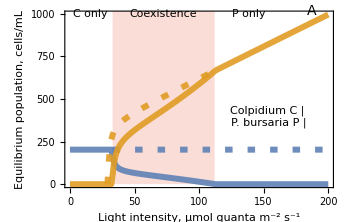

```mathematica
(*style for plot*)
cols=ColorData[97]/@{1,2};
legendstyle=11;
legendbifurcation=Framed[Grid[Table[{Style[{"Colpidium C","P. bursaria P"}[[i]],legendstyle,Italic],Plot[.5,{x,0,1},PlotStyle->{{Thickness[.14],cols[[i]]}},Axes->None,ImageSize->20,PlotRange->{0,1}]},{i,{1,2}}],Alignment->{Center,Center}],RoundingRadius->5,Background->White];
dashing1=Dashing[{.015,.03}];
dashing2=Dashing[.8{ .03,.064}];
thickness=Thickness[.012];
lightplotstyle={ImagePadding->{{65,45},{38,10}},LabelStyle->11,ImageSize->Medium,BaseStyle->{Opacity->0.9}};
(*plot bifurcation*)
plotA=ListPlot[{listc1,listc2,listp1,listp3(*,{{t2,0},{t3,0}},{{t2,0},{t3,0}}*)},Joined->True,PlotStyle->{{cols[[1]],thickness},{dashing1,cols[[1]],thickness},{cols[[2]],thickness},{dashing1,cols[[2]],thickness},{cols[[1]],thickness},{cols[[2]],dashing2,thickness}},Frame->{True,True,False,False},lightplotstyle,FrameLabel->{{"Equilibrium population, cells/mL",Null},{"Light intensity, μmol quanta m^-2 s^-1",Null}},PlotRange->Full,Epilog->Inset[legendbifurcation,Scaled[{.76,.4}]],PlotRangeClipping->{{True,True},{False,False}},ImagePadding->{{Automatic,105},{Automatic,Automatic}}
,LabelStyle->11,Prolog->{Lighter[ColorData[97][11],.8],Rectangle[{t2,0},{t3,1250}],Black,Inset[Style["Coexistence",11,FontFamily->"Arial"],{(t2+t3)/2,1000}],
Inset[Style["C only",11,FontFamily->"Arial"],{(t2+t3)/9.2,1000}],
Inset[Style["P only",11,FontFamily->"Arial"],{(t2+t3)/1.05,1000}],
Inset[Style["A",14,FontFamily->"Arial"],Scaled[{.92,1}]]}]
```

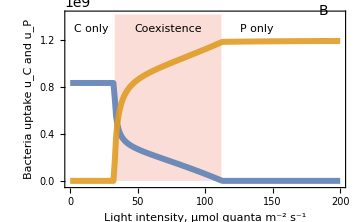
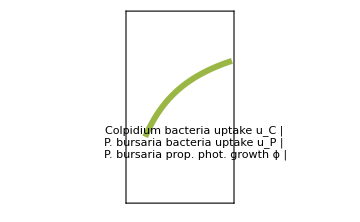

```mathematica
(*define functions for plotting derived quantities*)
h[a1_,a2_,h_][x1_,x2_][y1_,y2_]:=(a1 y1+a2 y2)/(1+a1 h x1+a2 h x2);
ub1=w1;
ub2=w2;
uc1=h[ac1,ac2,hc][b1,b2][b1,0] c;
uc2=h[ac1,ac2,hc][b1,b2][0,b2] c;
uc=uc1+uc2;
lc=mc c;
up1=h[ap1,ap2,hp][b1,b2][b1,0] p;
up2=h[ap1,ap2,hp][b1,b2][0,b2] p;
up=up1+up2;
lp=(1-l/(l+k))mp p;
addlight[list_]:=Table[{x[[1]],Join[{l->x[[1]]},#]&/@x[[2]]},{x,list}];
ps=l/(l+k)mp;
pbact=p (h[ap1,ap2,hp][b1,b2][b1,0]+h[ap1,ap2,hp][b1,b2][0,b2]);
cbact=c (h[ac1,ac2,hc][b1,b2][b1,0] +h[ac1,ac2,hc][b1,b2][0,b2]);
plotf=Piecewise[{{(ps p)/(yp pbact+ps p), p>0}, {0, True}}];
(*apply function to list (choosing equilbrium with pos)*)
getlist[f_,list_,pos_]:={#[[1]],f/.Sort[#[[2]],(p/.#1)≤(p/.#2)&][[pos]]/.testparspre[model]}&/@addlight[list];
getlistc[f_,list_,pos_]:={#[[1]],f/.Sort[#[[2]],(c/.#1)≤(c/.#2)&][[pos]]/.testparspre[model]}&/@addlight[list];
(*(*apply function to list (choosing equilbrium with pos)*)
getlistCondition[f_,list_,condition_]:={#[[1]],f/.Select[#[[2]],condition][[1]]/.testparspre[model]}&/@addlight[list];*)
(*apply functions to plot to lists*)
listgs=Table[Join[
getlist[f,lists[[1]],2],
getlistc[f,lists[[2]],3],
getlist[f,lists[[3]],-2],
getlist[f,lists[[4]],-1]
],{f,{plotf,pbact,cbact}}];
(*style for plots, legends*)
colPS=ColorData[97][3];
legendplot2=Framed[Grid[Table[{Style[{"Colpidium bacteria uptake u_C","P. bursaria bacteria uptake u_P","P. bursaria prop. phot. growth ϕ"}[[i]],.85legendstyle],Plot[.5,{x,0,1},PlotStyle->{{Thickness[.14],Join[cols,{colPS}][[i]](*,{None,None,Dashing[.3]}[[i]]*)}},Axes->None,ImageSize->20,PlotRange->{0,1}]},{i,3}],Alignment->{Center,Center}],RoundingRadius->5,Background->White];
(*plot up and uc*)
plot1=ListPlot[listgs[[{3,2}]],PlotStyle->({thickness,#}&/@cols),
Frame->{True,True,False,False},FrameStyle->{Automatic,Automatic,Automatic,Automatic},FrameLabel->{{"Bacteria uptake u_C and u_P",Null},{"Light intensity, μmol quanta m^-2 s^-1",Null}},PlotRange->{{0,200},{-.02,1}1.42 10^9},Evaluate@lightplotstyle,Joined->True,
Prolog->{Lighter[ColorData[97][11],.8],Rectangle[{t2,0},{t3,1.42 10^9}]},
PlotRangeClipping->False,
Epilog->{Black,Inset[Style["Coexistence",11,FontFamily->"Arial"],{(t2+t3)/2,1.3 10^9}],
Inset[Style["C only",11,FontFamily->"Arial"],{(t2+t3)/9.2,1.3 10^9}],
Inset[Style["P only",11,FontFamily->"Arial"],{(t2+t3)/1.05,1.3 10^9}],
Inset[Style["B",14,FontFamily->"Arial"],Scaled[{.92,1}]]}];
(*plot proportion of photosynthesis*)
plot2=ListPlot[Select[listgs[[1]],#[[2]]>0&],PlotStyle->{thickness,colPS},
Frame->{False,False,False,True},FrameLabel->{{Null,"Prop. phot. growth ϕ"},{Null,Null}},
PlotRange->{{0,200},{-.02,1}},Evaluate@lightplotstyle,FrameStyle->{Automatic,Automatic,Automatic,colPS},Epilog->Inset[legendplot2,Scaled[{.645,.315}]],
FrameTicks->{{None,All},{None,None}},Joined->True
];
(*show plots together*)
plotB=Overlay[{plot1,plot2}]
```

```mathematica
(*stack the bifurcations and export*)
(Export[outputdirectory<>"bifurcations-mech-model.pdf",#];
#)&@Column[{plotA,plotB}]
```

-Graphics-
-Graphics--Graphics-

```mathematica
(*Lotka-Volterra model*)
ClearAll["Global`*"]
(*directory for exporting plots*)
outputdirectory=NotebookDirectory[](*<>"export/"*);
(*name of model*)
model="lotka-volterra";
(*state variables*)
vars[model]={c,p};
(*function to find equilibria*)
equilibriumanalytical[model]=Solve[{(rc-lc (c+acp p)) c,
(r0+gmax l/(k+l)-lp (p+apc c)) p}==0,{c,p}];
(*parameter values: two stage fits*)
testparspre[model]=
Join[{rc->1.0561366576869755,lc->0.002285649007233084},
{r0->-0.11289976477539737,gmax->0.36370653565243405,lp->0.0000379683569540994,k->48.74401193564654},
{acp->0.35322869529826306,apc->3.1093871578986505},
{l->50}
];

(*find equilibria for range of light levels*)
list[model]=Table[{ll,Select[equilibriumanalytical[model]/.(testparspre[model]/.{(l->_)->(l->ll)}),(c/.#)>= 0∧(p/.#)>=0&]},{ll,Join[Range[0,35,1],Range[36,55,.1],Range[56,200,1]]}];
(*function to bring bifurcation list in right shape*)
extract[list_,var_]:=Flatten[Table[Table[{l[[1]],var/.x},{x,l[[2]]}],{l,list}],1];
(*find for which light levels there are 4 or more equilibria (to connect the right branches of the equilibria)*)
{t2,t3}=Select[list[model],Length[#[[2]]]≥4&][[{1,-1},1]];
(*first time when there are 3 or more equilibria*)
t1=Select[list[model],Length@#[[2]]≥3&][[1,1]];
(*conditions for choosing equilibria branches*)
conditions={#[[1]]<t1&,t1≤#[[1]]<t2&,t2≤#[[1]]≤t3&,t3<#[[1]]&};
(*seperate list of equilbria to multiple lists according to conditions*)
lists=Table[Select[list[model],cond],{cond,conditions}];
(*lists for Colpidium*)
listc1=Join[
{#[[1]],Max[c/.#[[2]]]}&/@lists[[1]],
{#[[1]],Max[c/.#[[2]]]}&/@lists[[2]],
{#[[1]],Max[c/.#[[2]]]}&/@lists[[3]]

];
listc2=Join[
{#[[1]],Sort[c/.#[[2]]][[3]]}&/@lists[[3]]
];
listc3=Join[
{#[[1]],Max[c/.#[[2]]]}&/@Join@@lists[[3;;4]]
];
listc4=Join[
{#[[1]],Min[c/.#[[2]]]}&/@lists[[4]]
];
(*lists for Paramecium*)
listp1=Join[
{#[[1]],Max[p/.#[[2]]]}&/@lists[[2]],
{#[[1]],Max[p/.#[[2]]]}&/@lists[[3]]
];
listp2=Join[
{#[[1]],Sort[p/.#[[2]]][[3]]}&/@lists[[3]]
];
listp3=Join[
{#[[1]],Max[p/.#[[2]]]}&/@lists[[3]],
{#[[1]],Max[p/.#[[2]]]}&/@lists[[4]]
];
listp4=Join[
{#[[1]],Min[p/.#[[2]]]}&/@Join@@lists[[1;;2]]
];
```

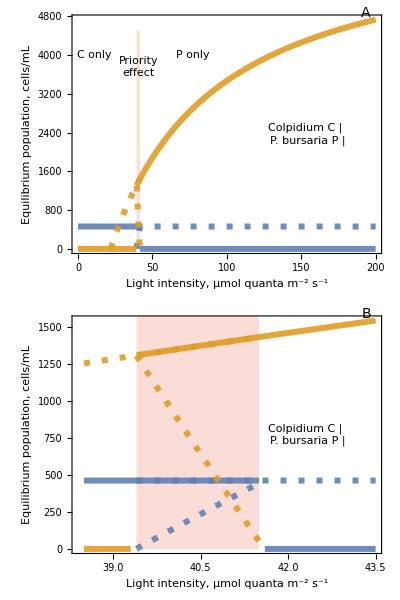

```mathematica
(*style for plot*)
cols=ColorData[97]/@{1,2};
legendstyle=11;
legendbifurcation=Framed[Grid[Table[{Style[{"Colpidium C","P. bursaria P"}[[i]],legendstyle,Italic],Plot[.5,{x,0,1},PlotStyle->{{Thickness[.14],cols[[i]]}},Axes->None,ImageSize->20,PlotRange->{0,1}]},{i,{1,2}}],Alignment->{Center,Center}],RoundingRadius->5,Background->White];
dashing1=Dashing[{.012,.024}];
dashing2=Dashing[.8{ .03,.064}];
thickness=Thickness[.012];
lightplotstyle={ImagePadding->{{65,45},{38,10}},LabelStyle->11,ImageSize->Medium,BaseStyle->{Opacity->0.9}};
(*plot bifurcation*)
plotLVbifurcation[zoom_,legendpos_,legendheights_,label_]:=ListPlot[Select[#,zoom[[1]]<= #[[1]]<=zoom[[2]]&]&/@{listc1,listc2,listc3,listc4,listp1,listp2,listp3,listp4(*,{{t2,0},{t3,0}},{{t2,0},{t3,0}}*)},Joined->True,PlotStyle->{{cols[[1]],thickness},{dashing1,cols[[1]],thickness},{dashing1,cols[[1]],thickness},{cols[[1]],thickness},{dashing1,cols[[2]],thickness},{dashing1,cols[[2]],thickness},{cols[[2]],thickness},{cols[[2]],thickness}(*,{cols[[1]],thickness},{cols[[2]],dashing2,thickness}*)},Frame->{True,True,False,False},lightplotstyle,FrameLabel->{{"Equilibrium population, cells/mL",Null},{"Light intensity, μmol quanta m^-2 s^-1",Null}},PlotRange->Full,Epilog->Inset[legendbifurcation,Scaled[{.76,.5}]],PlotRangeClipping->False(*{{True,True},{False,False}}*),ImagePadding->{{Automatic,105},{Automatic,Automatic}}
,LabelStyle->11,
Prolog->{Inset[Style[label,14,FontFamily->"Arial"],Scaled[{.95,1.01}]],Lighter[ColorData[97][11],.8],Rectangle[{t2,0},{t3,4500}],Black,Inset[Style["Priority\neffect",11,FontFamily->"Arial"],{legendpos[[2]](*(t2+t3)/2*),legendheights[[2]]}],
Inset[Style["StyleBox[\"C\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]only",11,FontFamily->"Arial"],{legendpos[[1]](*(t2+t3)/9.2*),legendheights[[1]](*1130*)}],
Inset[Style["StyleBox[\"P\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]only",11,FontFamily->"Arial"],{legendpos[[3]](*(t2+t3)/1.05*),legendheights[[1]](*1130*)}]}];
(Export[outputdirectory<>"L-V-bifurcations-two-stage.pdf",#];#)&@Column[{plotLVbifurcation[{0,200},{(t2+t3)/7.5,(t2+t3)/2,(t2+t3)/1.05},{4000,3750},"A"],
plotLVbifurcation[{38.5,43.5},{38.8,(t2+t3)/2,42.2},{1630,1580},"B"]}]
```

```mathematica
(*L-V bifurcation with single-stage fit*)
(*parameter values*)
testparspre[model]=
Join[{rc->0.9244406071544748,lc->0.0017937214626397883,acp->0.6245682852113703,r0->-0.12068127058231798,gmax->0.559039940138474,lp->0.0003001299992970003,apc->0.3607981586239132,k->54.328403163161425},
{l->50}
];
(*find equilibria for range of light levels*)
list[model]=Table[{ll,Select[equilibriumanalytical[model]/.(testparspre[model]/.{(l->_)->(l->ll)}),(c/.#)>= 0∧(p/.#)>=0&]},{ll,Join[Range[0,35,1],Range[36,55,.1],Range[56,200,1]]}];
(*function to bring bifurcation list in right shape*)
extract[list_,var_]:=Flatten[Table[Table[{l[[1]],var/.x},{x,l[[2]]}],{l,list}],1];
(*find for which light levels there are 4 or more equilibria (to connect the right branches of the equilibria)*)
{t2,t3}=Select[list[model],Length[#[[2]]]≥4&][[{1,-1},1]];
(*first time when there are 3 or more equilibria*)
t1=Select[list[model],Length@#[[2]]≥3&][[1,1]];
(*conditions for choosing equilibria branches*)
conditions={#[[1]]<t1&,t1≤#[[1]]<t2&,t2≤#[[1]]≤t3&,t3<#[[1]]&};
(*seperate list of equilbria to multiple lists according to conditions*)
lists=Table[Select[list[model],cond],{cond,conditions}];
(*lists for Colpidium*)
listc1=Join[
{#[[1]],Sort[c/.#[[2]]][[2]]}&/@Join@@lists[[1;;1]],
{#[[1]],Sort[c/.#[[2]]][[3]]}&/@Join@@lists[[2;;3]],
{#[[1]],Sort[c/.#[[2]]][[2]]}&/@lists[[4]]
];
listc2=Join[
{#[[1]],Max[c/.#[[2]]]}&/@Join@@lists[[2;;4]]
];
```

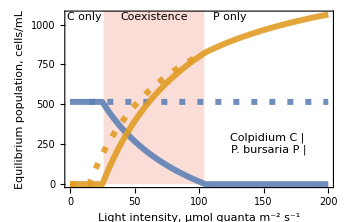

```mathematica
(*lists for Paramecium*)
listp1=Join[
{#[[1]],Max[p/.#[[2]]]}&/@Join@@lists[[1;;3]]
];
listp2=Join[
{#[[1]],Min[p/.#[[2]]]}&/@Join@@lists[[1;;2]],
{#[[1]],Sort[p/.#[[2]]][[3]]}&/@lists[[3]],
{#[[1]],Max[p/.#[[2]]]}&/@lists[[4]]
];
(*style for plot*)
cols=ColorData[97]/@{1,2};
legendstyle=11;
legendbifurcation=Framed[Grid[Table[{Style[{"Colpidium C","P. bursaria P"}[[i]],legendstyle,Italic],Plot[.5,{x,0,1},PlotStyle->{{Thickness[.14],cols[[i]]}},Axes->None,ImageSize->20,PlotRange->{0,1}]},{i,{1,2}}],Alignment->{Center,Center}],RoundingRadius->5,Background->White];
dashing1=Dashing[{.012,.024}];
dashing2=Dashing[.8{ .03,.064}];
thickness=Thickness[.012];
lightplotstyle={ImagePadding->{{65,45},{38,10}},LabelStyle->11,ImageSize->Medium,BaseStyle->{Opacity->0.9}};
(*plot bifurcation*)
plotLVbifurcation[zoom_,legendpos_,legendheights_]:=ListPlot[Select[#,zoom[[1]]<= #[[1]]<=zoom[[2]]&]&/@{listc1,listc2,listp1,listp2},Joined->True,PlotStyle->{{cols[[1]],thickness},{dashing1,cols[[1]],thickness},{dashing1,cols[[2]],thickness},{cols[[2]],thickness}},Frame->{True,True,False,False},lightplotstyle,FrameLabel->{{"Equilibrium population, cells/mL",Null},{"Light intensity, μmol quanta m^-2 s^-1",Null}},PlotRange->Full,Epilog->Inset[legendbifurcation,Scaled[{.76,.25}]],PlotRangeClipping->{{True,True},{False,False}},ImagePadding->{{Automatic,105},{Automatic,Automatic}}
,LabelStyle->11,Prolog->{Lighter[ColorData[97][11],.8],Rectangle[{t2,0},{t3,4500}],Black,Inset[Style["Coexistence",11,FontFamily->"Arial"],{legendpos[[2]],legendheights[[2]]}],
Inset[Style["StyleBox[\"C\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]only",11,FontFamily->"Arial"],{legendpos[[1]],legendheights[[1]]}],
Inset[Style["StyleBox[\"P\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]only",11,FontFamily->"Arial"],{legendpos[[3]],legendheights[[1]]}]}]
(Export[outputdirectory<>"L-V-bifurcations-single-stage.pdf",#];#)&@plotLVbifurcation[{0,200},{(t2+t3)/11.5,(t2+t3)/2,(t2+t3)/1.05},{1050,1050}]
```